# Lab 7 William Keilsohn Section 32 4/24/2013

Question 1: Define the function a(n), then find numerical values to evalute the the convergence of its series using the ratio test with the large values of n given.

```mathematica
a[n_]=Factorial[n]/n^n
```

n^-n n!

```mathematica
A[n_]=a[n]/a[n+1]
```

(n^-n (1+n)^(1+n) n!)/((1+n)!)

```mathematica
A[1000.]
```

2.7169239322

```mathematica
A[10000.]
```

2.718145927

```mathematica
A[100000.]
```

2.71826824

Since all large values for a(n+1)/a(n) are greater than one, the series that corosponds to a(n) from n=0 to Infinity is mostlikely divergent. The value for the limit as n approaches infinity of a(n+1)/a(n) is most likely 2.7183. As stated, this value would imply that the series is divergent.

Question 2: Plot the cos(x) function and the Taylor series over the interval [-8,8] with the Tsylor series in degree 4. Use different colors for each. At what values is the Taylor series a good aproximation and at what values is it a bad one? Try using the Taylor function in degrees 8,12,and 16. When do these make good approximations?

```mathematica
f[x_]=Cos[x]
```

Cos[x]

```mathematica
T4[x_]=Sum[(-1)^n/Factorial[2*n]*x^(2*n),{n,0,4/2.}]
```

1-x^2/2+x^4/24

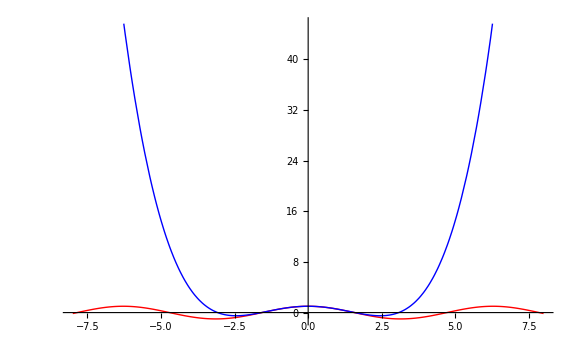

```mathematica
Plot[{f[x],T4[x]},{x,-8,8},PlotStyle->{Red,Blue}]
```

Based on the above graph, the Taylor series of degree 4 is a good aproximation of Cos(x) for x values [-2,2]. It is not a good approximation for (-Infinity, -2)U(2,Infinity).

```mathematica
T8[x_]=Sum[(-1)^n/Factorial[2*n]*x^(2*n),{n,0,8/2.}]
```

1-x^2/2+x^4/24-x^6/720+x^8/40320

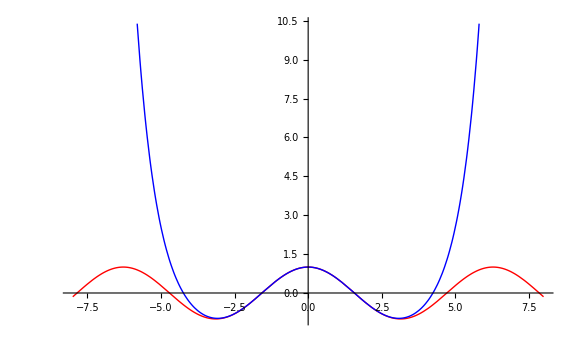

```mathematica
Plot[{f[x],T8[x]},{x,-8,8},PlotStyle->{Red,Blue}]
```

Based on the graph, one can conclude that the Taylor series with degree 8 is a good approximation of Cos(x) for x values in the interval [-3,3] and is a bad approximation for x values in (-Infinity,-3)U(3,Infinity).

```mathematica
T12[x_]=Sum[(-1)^n/Factorial[2*n]*x^(2*n),{n,0,12/2.}]
```

1-x^2/2+x^4/24-x^6/720+x^8/40320-x^10/3628800+x^12/479001600

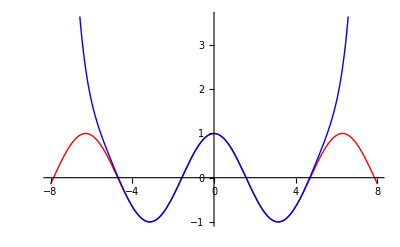

```mathematica
Plot[{f[x],T12[x]},{x,-8,8},PlotStyle->{Red,Blue}]
```

Based on the graph, one can conlude that the Taylor series with degree 12 is a good approximation for Cos(x) for x values in [-5,5] and is a bad approximation for x values in (-Infinity,-5)U(5,Infinity).

```mathematica
T16[x_]=Sum[(-1)^n/Factorial[2*n]*x^(2*n),{n,0,16/2.}]
```

1-x^2/2+x^4/24-x^6/720+x^8/40320-x^10/3628800+x^12/479001600-x^14/87178291200+x^16/20922789888000

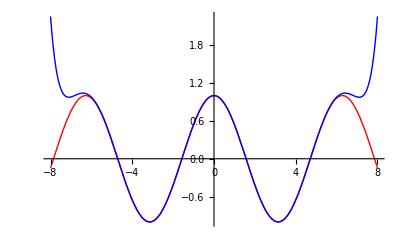

```mathematica
Plot[{f[x],T16[x]},{x,-8,8},PlotStyle->{Red,Blue}]
```

Based on the graphn one can conclude that the Taylor series with degree 16 is a good approximation for Cos(x) for x values in [-6,6] and is a bad approximation for x values in (-infinity,-6)U(6,Infinity).